# Mathematica Advanced Lesson 4 Graphics Dr. Dale R. Doty University of Tulsa

## Two-Dimensional Plots:

Evaluate (Shift-Enter) the following Input Cell to clear and remove any existing definitions from memory before you start this lesson.

```mathematica
Remove["Global`*" ]
```

### Plot:

The basic command to generate a two-dimensional plot is "Plot".

Plot[ f[x], {x, xmin, xmax}]  
 
generates a plot of f[x] as a function of x from xmin to xmax.

```mathematica
Plot[

Sin[x],

{x,0,2π}

]
```

Generate a plot of a list of functions:  

	{Sin[x],Sin[2x],Sin[3x]}

Plot[{f1[x], f2[x], ... }, {x, xmin, xmax}]  
 
plots several functions fi[x].

```mathematica
Plot[

{Sin[x],Sin[2x],Sin[3x]},

{x,0,2π}

]
```

### Options:

There are many options available for the Plot[...] command.

```mathematica
Column[

Options[

Plot

]

]
```

We will look at a few of the more useful options to see how they influence the appearance of the graph.

### Example using Plot options:

Consider the following Plot of  1/x  for  -1 ≤ x ≤ 1  which uses only default settings:

```mathematica
Plot[1/x,{x,-1,1}]
```

Although the graph generated above is reasonable considering that the function becomes infinite at  x = 0, its appearance could be improved by restricting the plot's vertical range.  This can be accomplished by using the PlotRange option:

PlotRange  
 
is an option for graphics functions that specifies what points to include in a plot.

Restrict the vertical PlotRange to be between -6 and 6:

```mathematica
Plot[

1/x,

{x,-1,1}, 

PlotRange->{-6,6}

]
```

The appearance of the above graph may or may not be more desirable.

Note, it is also possible to have the range of the graph  -2 ≤ x ≤ 2   different from the plot  -1 ≤ x ≤ 1

```mathematica
Plot[

1/x,

{x,-1,1},

PlotRange->{{-2,2},{-6,6}}

]
```

Eventually, you will want to alter the appearance of the curve contained within the plot.  Specifically, you would like to alter the style of the plot curve.  This can be accomplished with the PlotStyle option.

PlotStyle  
 
is an option for Plot and ListPlot that specifies the style of lines or points to be plotted.

One style is to alter the thickness of the curve.

Thickness[r]  
 
is a graphics directive which specifies that lines which follow are to be drawn with a thickness r. 
The thickness r is given as a fraction of the total width of the graph.

As an example, increase the thickness of the curve to be 2% of the total size of the graph:

```mathematica
Plot[

1/x,

{x,-1,1},

PlotRange->{-6,6},
PlotStyle->Thickness[.02]

]
```

The above thickness is excessive, maybe a thickness of .01 or .005 would be better.

Another style is to apply dashing to the curve.

Dashing[{r1, r2, ... }]  
 
is a two-dimensional graphics directive which specifies that lines which follow are to be drawn dashed, with successive segments of lengths r1, r2, ...  (repeated cyclically). 
The ri is given as a fraction of the total width of the graph."

As an example, apply dashing to the curve to be 3% "dash" followed by 2% "blank" of the total size of the graph:

```mathematica
Plot[

1/x,

{x,-1,1},

PlotRange->{-6,6},
PlotStyle->{Thickness[.01],Dashing[{.03,.02}]}

]
```

Another option is to apply GridLines and/or a Frame to our graph:

Frame  
 
is an option for two-dimensional graphics functions which specifies whether a frame should be drawn around the plot.

GridLines  
 
is an option for two-dimensional graphics functions that specifies grid lines.

Automatic

represents an option or other value that is to be chosen automatically by a built-in function.

```mathematica
Plot[

1/x,

{x,-1,1},

PlotRange->{-6,6},
PlotStyle->{Thickness[.01],Dashing[{.03,.02}]},
GridLines->Automatic,
Frame->True

]
```

Another option is to apply a background color to our graph:

Background  
 
is an option which specifies the background color to use.

GrayLevel[level]  
 
is a graphics directive which specifies the gray-level intensity with which graphical objects that follow should be displayed.

Hue[h]  
 
is a graphics directive which specifies that graphical objects which follow are to be displayed, if possible, in a color corresponding to hue h.
Hue[h, s, b] specifies colors in terms of hue, saturation and brightness.

RGBColor[red, green, blue]
 
is a graphics directive which specifies that objects which follow are to be displayed, if possible, in the color given.

```mathematica
Plot[

1/x,

{x,-1,1},

PlotRange->{-6,6},
PlotStyle->{Thickness[.01],Dashing[{.03,.02}]},
GridLines->Automatic,
Frame->True,
Background->GrayLevel[0.9]

]
```

Another option is to restrict the plot region of our graph (i.e. shrink the graph so that it does not expand to the outer edges of our plot region):

PlotRegion  
 
is an option for graphics functions that specifies what region of the final display area a plot should fill.

```mathematica
Plot[

1/x,

{x,-1,1},

PlotRange->{-6,6},
PlotStyle->{Thickness[.01],Dashing[{.03,.02}]},
GridLines->Automatic,
Frame->True,
Background->GrayLevel[0.9],
PlotRegion->{{.05,.95},{.05,.95}}

]
```

Apply a PlotLabel to our graph:

PlotLabel  
 
is an option for graphics functions that specifies an overall label for a plot.

```mathematica
Plot[

1/x,

{x,-1,1},

PlotRange->{-6,6},
PlotStyle->{Thickness[.01],Dashing[{.03,.02}]},
GridLines->Automatic,
Frame->True,
Background->GrayLevel[0.9],
PlotRegion->{{.05,.95},{.05,.95}},
PlotLabel->"Plot of: 1/x"

]
```

Apply a style to the plot label:

Style[expr, options]  
 
prints using the specified style options.

Style[expr, "style"]  
 
prints using the specified cell style in the current notebook.

```mathematica
Plot[

1/x,

{x,-1,1},

PlotRange->{-6,6},
PlotStyle->{Thickness[0.01],Dashing[{0.03,0.02}]},
GridLines->Automatic,
Frame->True,
Background->GrayLevel[0.9],
PlotRegion->{{0.05,0.95},{0.05,0.95}},
PlotLabel->
Style[
"Plot of: 1/x",
FontFamily->"Arial",
FontSize->14,
FontWeight->"Bold",
FontSlant->"Italic"
]

]
```

Apply an axis label and/or frame label to our graph:

AxesLabel  
 
is an option for graphics functions that specifies labels for axes.

FrameLabel  
 
is an option for two-dimensional graphics functions that specifies labels to be placed on the edges of a frame around a plot.

```mathematica
Plot[

1/x,

{x,-1,1},

PlotRange->{-6,6},
PlotStyle->{Thickness[0.01],Dashing[{0.03,0.02}]},
GridLines->Automatic,
Frame->True,
Background->GrayLevel[0.9],
PlotRegion->{{0.05,0.95},{0.05,0.95}},
PlotLabel->
Style[
"Plot of: 1/x",
FontFamily->"Arial",
FontSize->14,
FontWeight->"Bold",
FontSlant->"Italic"
],
AxesLabel->{"X",None},
FrameLabel->{"Label X values here","Label Y values here",None,None}

]
```

### Warning: Extreme Example! Use many Plot options together:

Consider one last example which brings everything together:    Plot:    ∫1/x ⅆx

```mathematica
Plot[

Evaluate[∫1/x ⅆx],

{x,0.1,10},

PlotRange->{{0,10},{-3,3}},
PlotStyle->{Thickness[0.01],Dashing[{0.03,0.02}]},
GridLines->Automatic,
Frame->True,
Background->GrayLevel[0.9],
PlotRegion->{{0,1},{0.01,1}},
PlotLabel->
Style[
Row[{"Plot of: ",HoldForm[∫1/x ⅆx]}],
FontFamily->"Arial",
FontSize->12,
FontWeight->"Bold"
],
AxesLabel->{"X",None},
FrameLabel->{"FrameLabel X values here","Y values here",None,None}

]
```

The above graph is extremely complicated in nature, much more than what you would normally need.  However, it illustrates many of the plotting options.

### Help! Do You Really Expect Me To Remember All of This?

No I do not!

What I EXPECT is that you will visit the Help Documentation Center any time you have a complicated plot.

For example, say that you want a more detailed plot label for the following plot and you have no idea how to do it.

```mathematica
Plot[

Sin[2π x],{x,0,1},

PlotLabel->Sin[2π x]

]
```

Kind of a pathetic plot label isn't it.

So, go to the Help Documentation Center and enter "plot label" and follow the links.

Go through the examples until you hit upon something you can use:

-Graphics-

Copy and Paste this into your code:

```mathematica
Plot[

Sin[2π x],{x,0,1},

PlotLabel->Style[Framed[y^3<x^2+x],16,Blue,Background->Lighter[Yellow]]

]
```

Then modify the above code to meet your specific needs:

```mathematica
Plot[

Sin[2π x],{x,0,1},

PlotLabel->Style[Framed[Sin[2π x]],18,Darker[Blue],Bold,Background->None]

]
```

Remember, you can not hope to know and understand all of the options available in Mathematica. Therefore, you must learn to search through examples to find something close to what you really want. Then copy, paste and modify to meet your needs.

## Show Command:

Mathematica generates a PostScript description of each graph that is generated in your notebook.  It is possible to save the PostScript description and show it later.  Even more important, it is possible to combine several different graphs together using the show command.  The general outline is as follows:

	plot1 = Plot[...]
	
	...  some code  ...
	
	plot2 = Plot[...]
	
	...  some code  ...
	
	plot3 = Plot[...]
	
	...  some code  ...
	
	Show[ plot1, plot2, plot3 ]

### Example:

```mathematica
plot1=Plot[Sin[2π x],{x,0,1}]
```

```mathematica
plot2=Plot[Cos[2π x],{x,0,1}]
```

```mathematica
plot3=Plot[ ⅇ^x ,{x,0,1}]
```

Show[g1, g2, ... ]  
 
shows several plots combined.

```mathematica
Show[plot1,plot2,plot3,PlotRange->All]
```

Observe that even though the range of plot3 was different than the range of plot1 and plot2, the Show[...] command combined them together correctly.

What is even more surprising is that the Show[...] command can combine any type of 2D graphics together automatically.  The following section will show how a Plot[...] and a ListPlot[...] can be combined automatically.

## ListPlot and ParametricPlot:

### ListPlot:

Consider the following problem:  
	1: Generate some data with random noise
	2: Plot the list of data using ListPlot[...]
	3: Find the linear quadratic least squares fit to the data
	4: Plot the least squares function using Plot[...]
	5: Show the ListPlot and the Plot together using the Show[...] command
	
To create some data, we will generate a list (i.e. table) of numbers corresponding to a quadratic function with some random noise.

RandomReal[ ]  
 
gives a uniformly distributed pseudorandom Real in the range 0 to 1.

```mathematica
someData=

Table[

{0.1 i,(0.1 i)^2+0.5 (RandomReal[]-0.5)},

{i,1,20}

]
```

We can plot this list of data using just the  y  coordinate vs. its number location within the list (i.e. 1, 2, 3, etc.) or we can plot a list of  {x,y}  data points:

ListPlot[{y1, y2, ... }]   

plots a list of values. The x coordinates for each point are taken to be 1, 2, ... .

ListPlot[{{x1, y1}, {x2, y2}, ... }]   

plots a list of values with specified x and y coordinates.

Plot this list of  {x, y}  data points data using ListPlot[...]:

```mathematica
ListPlot[someData]
```

The appearance can be improved by applying a PlotStyle to increase the PointSize:

PlotStyle  

is an option for Plot and ListPlot that specifies the style of lines or points to be plotted.

PointSize[d]  

is a graphics directive which specifies that points which follow are to be shown if possible as circular regions with diameter d. 
The diameter d is given as a fraction of the total width of the graph.

```mathematica
plot1=

ListPlot[

someData,

PlotStyle->{PointSize[0.02]}

]
```

Observe that the list plot information has been stored in "plot1".

It is now easy to determine a least squares linear fit to our data set.

Fit[data, funs, vars]      

finds a least-squares fit to a list of data as a linear combination of the functions funs of variables vars.

```mathematica
Clear[f,x]
```

```mathematica
f[x_]=Fit[someData,{1,x,x^2},x]
```

Observe what is stored in "f":

```mathematica
?f
```

Plot our least squares quadratic fit to the data using Plot[...].

```mathematica
plot2=

Plot[

f[x],

{x,0,2}, 

PlotStyle-> {Thickness [.009]}

]
```

Observe that the plot information has been stored in "plot2".

Mathematica has a common form for storing 2-dimensional graphs of different types.  Therefore we can "show" both our ListPlot of the data and our continuous Plot of the function on one graph.

Show[g1, g2, ... ]      

shows several plots combined.

```mathematica
Show [plot1, plot2]
```

### ParametricPlot:

ParametricPlot[ {fx[t], fy[t]}, {t, tmin, tmax}]     
 
produces a parametric plot with x and y coordinates fx[t] and fy[t] generated as a function of t.

```mathematica
ParametricPlot[

{Cos[θ],Sin[θ]},

{θ,0,2 π},

PlotStyle->{Thickness[.009],Orange}

]
```

### Warning: Extreme Example! Show[ ParametricPlot[ ... ], Plot[ ... ] ]

Use the Show[ ... ] command to combine two very different and very intricate 2-D plots:

	plot1=ParametricPlot[ ... ]
	
and

	plot2=Plot[ ... ]

How about a 2-D parametric plot with intricate color shading:

Mesh

is an option for that specifies what mesh should be drawn.

MeshFunctions

is an option for plotting functions that specifies functions to use to determine the placement of mesh divisions.

MeshShading

is an option for plotting functions that gives lists of colors to use for regions between mesh divisions.

MeshStyle

is an option for plotting functions that specifies the style in which to draw a mesh.

AspectRatio      

is an option for Show and related functions which specifies the ratio of height to width for a plot.

```mathematica
plot1=

ParametricPlot[{u/2 Cos[u]+4,-u/15 Sin[u]},{u,0,4Pi},

PlotStyle->{Thickness[0.01]},
Mesh->20,
MeshShading->Table[Hue[i],{i,0,1,.05}],
MeshStyle->{PointSize[.02],Orange},
AspectRatio->1

]
```

How about a standard 2-D plot with colored filling:

Filling

is an option for plot functions which specifies what filling to add under points, curves and surfaces.

```mathematica
plot2=

Plot[

Evaluate[

Table[BesselJ[n,x],{n,4}]

],

{x,0,10},

Filling->Axis

]
```

Use the Show[ ... ] command to combine the two 2-D plots:

	plot1=ParametricPlot[ ... ]
	
and

	plot2=Plot[ ... ]

```mathematica
Show[plot1,plot2]
```

## Three-Dimensional Plots:

### Plot3D:

It is also possible to generate a 3 dimensional plot over a rectangular domain using the command Plot3D.

Plot3D[ f[x,y], {x, xmin, xmax}, {y, ymin, ymax}]      

generates a three-dimensional plot of f as a function of x and y.

```mathematica
Plot3D[

Sin[x*y],

{x,0,π},
{y,0,π}

]
```

Just for fun, click your mouse on the above plot and rotate it to see the "bottom" side of the plot.

### Options:

There are many options available for the Plot3D[...] command.

```mathematica
Column[

Options[

Plot3D

]

]
```

### ContourPlot:

It is also possible to generate a contour plot over a rectangular domain using the command ContourPlot.

ContourPlot[ f[x,y], {x, xmin, xmax}, {y, ymin, ymax}]     

generates a contour plot of f as a function of x and y.

```mathematica
ContourPlot[

Sin[x*y],

{x,0,π},
{y,0,π},

PlotPoints->30

]
```

### DensityPlot:

It is also possible to generate a density plot over a rectangular domain using the command DensityPlot.

DensityPlot[ f[x,y], {x, xmin, xmax}, {y, ymin, ymax}]   
  
makes a density plot of f as a function of x and y.

```mathematica
DensityPlot[

Sin[x*y],

{x,0,π},
{y,0,π},

PlotPoints->50

]
```

### ParametricPlot3D:

Of course, more complicated functions have more interesting shapes:

ParametricPlot3D[{f_x[u],f_y[u],f_z[u]},{u,u_min,u_max}]
produces a three-dimensional space curve parametrized by a variable u which runs from u_min to u_max.

ParametricPlot3D[{f_x[u,v],f_y[u,v],f_z[u,v]},{u,u_min,u_max},{v,v_min,v_max}]
produces a three-dimensional surface parametrized by u and v.

```mathematica
ParametricPlot3D[

{
1.16^v Cos[v] (1+Cos[u]),
-1.16^v Sin[v] (1+Cos[u]),
-2 1.16^v (1+Sin[u])
},

{u,0,2 π},
{v,-15,6},

Mesh->False,
PlotRange->All,
PlotPoints->40

]
```

Just for fun, click your mouse on the above plot and rotate it to see the "back" side of the plot.

### Warning: Extreme Example! Show[ ParametricPlot3D[ ... ], Plot3D[ ... ] ]

Use the Show[ ... ] command to combine two very different 3-D plots:

	plot1=ParametricPlot3D[ ... ]
	
and

	plot2=Plot3D[ ... ]

```mathematica
plot1=

ParametricPlot3D[

{
1.16^v Cos[v] (1+Cos[u]),
-1.16^v Sin[v] (1+Cos[u]),
-2 1.16^v (1+Sin[u])
},

{u,0,2 π},
{v,-15,6},

Mesh->False,
PlotRange->All,
PlotPoints->40

]
```

```mathematica
plot2=

Plot3D[

Sin[x*y]-5,

{x,0,π},
{y,0,π}

]
```

Use the Show[ ... ] command to combine two different 3-D plots:

	Show[ plot1, plot2 ]

```mathematica
Show[plot1,plot2]
```

Just for fun, click your mouse on the above plot and rotate it to see inside the "mouth" of the plot.

## Drawing Tools and the Graphics Inspector:

If you have ever used the Microsoft Paint program contained in the Windows operating system, then using Mathematica's "Drawing Tools" and "Graphics Inspector" should be a very straight forward experience.

In general, you should generate the basic plot using one of Mathematica's plotting commands like Plot[ ... ], Plot3D[ ... ], ParametricPlot[ ... ] etc. Then, you can modify your plot using the "Drawing Tools" and "Graphics Inspector".

Step 1:  Load the "Drawing Tools" and "Graphics Inspector":

	Menu Bar >> Graphics >> Drawing Tools

	Menu Bar >> Graphics >> Graphics Inspector

|

Step 2:  Type:

	Plot[Sin[x], {x, 0, 2 π}]   
	
into an Input Cell within a Mathematica window and evaluate to generate a plot of the sine curve.

```mathematica
Plot[Sin[x],{x,0,2 π}]
```

Step 3:  	Place the mouse cursor over the plot and click to select the plot.
		(Note the orange outline box surrounding the plot.)

		Place the mouse cursor over the sine curve within the plot and click several times until selected.
		Note the appearance of    ♢+adjacent to the cursor when you are over the selected sine curve and
		also note several nested orange outline boxes as illustrated below.
  
			Then adjust the Thickness and Dashing for the curve as indicated below :

Step 4:  Add some text to you plot:

	Select    in 2 D Drawing:

		Point the mouse cursor to where you want the text to be located within the plot 
		and click to select the text location:

			Then type your text into your plot as shown below.
   
   				You may use Menu >> Format >> Font, Face, Size, etc. to
				edit the appearance of the text after it has been typed into the plot.
				Just remember to click several times on the text to make sure it is selected
				before you attempt to edit your text.

### Warning: Extreme Example!

Play arround with your plot to create whatever image that you want:

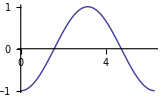
```mathematica
-Graphics-
-Graphics-
```

Observe that you have great flexibility to create dramatic plots!

## Other Graphics:

The graphing capability displayed above illustrates only a small portion of what is available within Mathematica.  Not only are other types of graphics available, but Mathematica has add-on packages which extend the basic graphing capability.  If you have specialized needs, consult the Help Documentation Center for additional information.

## Manipulate: Dynamic Plots:

Manipulate[expr,{u,u_min,u_max}]
generates a version of expr with controls added to allow interactive 
manipulation of the value of u.

Manipulate[expr,{u,u_min,u_max,du}]
allows the value of u to vary between u_min and u_max in steps du.

Manipulate[expr,{{u,u_init},u_min,u_max,…}]
takes the initial value of u to be u_init.

Manipulate[expr,{{u,u_init,u_lbl},…}]
labels the controls for u with u_lbl.

Manipulate[expr,{u,{u_1,u_2,…}}]
allows u to take on discrete values u_1,u_2,….

Manipulate[expr,{u,…},{v,…},…]
provides controls to manipulate each of the u,v,….

### Introduction to Manipulate[...]

The single command Manipulate lets you create an astonishing range of interactive applications with just a few lines of input. Manipulate is designed to be used by anyone who is comfortable using basic commands such as Table and Plot: it does not require learning any complicated new concepts, nor any understanding of user interface programing ideas.

The output you get from evaluating a Manipulate command is an interactive object containing one or more controls (sliders, etc.) that you can use to vary the value of one or more parameters. The output is very much like a small applet or widget: it is not just a static result, it is a running program you can interact with.

At its most basic, the syntax of Manipulate is identical to that of the humble function Table. 

Consider this Table command, which produces a list of numbers from 1 to 20 in steps of 1.

```mathematica
Table[n,{n,1,20,1}]
```

Simply replace the word Table with the word Manipulate, and you get an interactive application that lets you explore values of n from 1 to 20 in steps of 1 with a slider.

```mathematica
Manipulate[n,{n,1,20,1}]
```

Move the above Slider bar and see what happens.

Of course the whole point of Manipulate (and Table for that matter) is that you can put any expression you like into the first argument, not just a simple variable name. 

One way to think of Manipulate is as a way to interactively explore a large parameter space. You can move around that space at will, exploring interesting directions as they appear. 

Manipulate supports a wide range of alternate ways of specifying variables, which generate different kinds of controls for those variables. These dynamic controls include checkboxes, popup menus, and others in addition to sliders. 

The principle is that for each Dynamic variable, u, you ask for a particular set of possible values for the variable u (like from 1 to 20 in steps of 1 e.g. {u,1,20,1}) and Manipulate automatically chooses an appropriate type of control to make those values conveniently available.

	Possible Values that you want:	Manipulate Automatically Chooses an Appropriate Type of Control:
	{u,u_min,u_max} |  			continuous manipulator (slider, animator, etc.)
	{u,u_min,u_max,du} |    			discrete manipulator with step du
	{u,{x_min,y_min},{x_max,y_max}}		2D slider
	{u,Locator}				a locator in a graphic
	{u,{u_1,u_2,…}}			setter bar for few elements; popup menu for more
	etc.					etc.
	etc.					etc.

### Example 1

Manipulate[
	
	  Plot[ Sin[ n 2 Pi x ] , {x, 0, 1}] ,  ⟸ Dynamic expr[ n ] you want to control  
 	
	  { n, 1, 5} ,   ⟸ continuous Slider control of n from 1 to 5

	]

Evaluate the following code and move the Slider to see what happens:

```mathematica
Manipulate[

Plot[Sin[n 2π x],{x,0,1}],

{n,1,5}

]
```

As illustrated in the figure shown below, click on the various open/close "+" buttons in the above Output Cell and experiment with each of the available options.

### Example 2

Dynamic Plot of Sin[ a x + b ] with 2 Sliders Dynamically Manipulating the values of a and b:

Manipulate[
	
	  Plot[ a x + b, {x, 0, 2Pi}] ,  ⟸ Dynamic expr[ a, b ] you want to control  
 	
	  { a, 1, 5} ,   ⟸ continuous Slider control of a from 1 to 5

	  { b, 0, 2Pi, Pi/2}	⟸ discrete Slider control of b from 0 to 2π in discrete steps of π/2

	]
	
Evaluate:

```mathematica
Manipulate[

Plot[Sin[a x+b],{x,0,2π}],

{a,1,5},

{b,0,2π,π/2}

]
```

Slowly move both of the above Slider bars to see what happens.

### Example 3

The Dynamic Control is a PopUp Menu for the 6 functions: {Sin, Cos, Tan, Cot, Sec, Csc}

Manipulate[
	
	  Plot[ f [x], {x, 0, 2Pi}] ,  ⟸ Dynamic expr[ f ] you want to control  
 	
	  { f, {Sin, Cos, Tan, Cot, Sec, Csc}} ,   ⟸ popup menu control of f for 6 functions

	]
	
Evaluate:

```mathematica
Manipulate[

Plot[f[x],{x,0,2π},PlotLabel->f],

{f,{Sin,Cos,Tan,Cot,Sec,Csc}}

]
```

### Example 4 Warning: Extreme Example!

The following code illustrates how EASY it is to create EXTREMELY COMPLICATED DYNAMIC expressions in Mathematica:

	Manipulate[expr,  ... controls and annotations ... ]

	Step 1: Add the expr to be Dynamically Manipulated containing the
	
		Six Variables :   a1 , n1, p1, a2, n2, p2
	
		The Dynamic expression containing the six variables is a ParametricPlot[ ... ]:
		
			ParametricPlot[
{
a1 Sin[n1 (x+p1)],
a2 Cos[n2 (x+p2)]
},
{x,0,20Pi},
PlotRange→1,
PerformanceGoal→"Quality"
]
	
	Step 2: Add six Dynamic Continuous Sliders (each with an initital value and a name) 
	             separated by a Delimiter:
	
		{{n1,1,"Frequency"},1,4},

{{a1,1,"Amplitude"},0,1},

{{p1,0,"Phase"},0,2Pi},

Delimiter,

{{n2,5/4,"Frequency"},1,4},

{{a2,1,"Amplitude"},0,1},

{{p2,0,"Phase"},0,2Pi}

	Step 3: Add two Dynamic annotations (i.e. Plots[ ... ]) to be Manipulated by the Sliders:
	
		Dynamic[
ParametricPlot[
{a1 Sin[n1 (x+p1)],x},
{x,0,2Pi},
ImageSize→100,
AspectRatio→1,
PlotRange→{{-1,1},{0,2Pi}}
]
]
		
		Dynamic[
Plot[
a2 Sin[n2 (x+p2)],
{x,0,2Pi},
ImageSize→100,
AspectRatio→1,
PlotRange→1
]
]
		
	Step 4: Place the Controls to the Left of the Dynamically Manipulated expression i.e. ParametricPlot[...]:
	
		ControlPlacement→Left
		
	Step 5: Then evaluate your code:

```mathematica
Manipulate[

ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20Pi},PlotRange->1,PerformanceGoal->"Quality"],

Dynamic[ParametricPlot[{a1 Sin[n1 (x+p1)],x},{x,0,2Pi},ImageSize->100,AspectRatio->1,PlotRange->{{-1,1},{0,2Pi}}]],

{{n1,1,"Frequency"},1,4},

{{a1,1,"Amplitude"},0,1},

{{p1,0,"Phase"},0,2Pi},

Delimiter,

Dynamic[Plot[a2 Sin[n2 (x+p2)],{x,0,2Pi},ImageSize->100,AspectRatio->1,PlotRange->1]],

{{n2,5/4,"Frequency"},1,4},

{{a2,1,"Amplitude"},0,1},

{{p2,0,"Phase"},0,2Pi},

ControlPlacement->Left
]
```

Move the above 6 Sliders and have fun!

And while you are having fun, think about how much code would be required in any other programing language to generate the above dynamic expression.

Remember, the command Manipulate[ expr, ... ] works on ANY expression, and not just on a plot.

## Exercises Advanced Lesson 4

Your Name:

Your Math Class:

Note: Some of the following exercises are expressed in every day mathematical notation rather than proper Mathematica notation.  You MUST convert every day notation into Mathematica notation for your code to work properly.  For example:

	Equations must be changed from  "="  to  "=="  to work correctly (i.e. x^2==2x  not  x^2=2x  ).  
	Functions must be expressed as  f[x]  and  not  f(x)  to work correctly.  
	Functions must be defined using  "_"  to work correctly (i.e.  f[x_]=2 x^2+1  and not  f[x]=2 x^2+1).
	Mathematica functions must start with a capital (i.e.  Sin[x]  not  sin[x]).
	Your functions should start with a lower case letter (i.e.  f[x]  not  F[x]).
	Special symbols must be entered correctly (i.e.  ⅇ  from the palette and not  e ).
	
These exercises begin your training in making this conversion automatically.

Remember to clear all variables that you will use below:  Clear[          ...             ]

1: Using the existing code in Mathematica's Help Documentation Center can make your work much easier.
Part1: Open Mathematica's Help Documentation Center.
Part2: Look up ParametricPlot.
Part3: Open each and every example and see what all of the examples look like.
Part4: Under Option>> MeshShading, choose your favorite example of MeshShading and Copy and Paste the corresponding Mathematica Code into your notebook and then evaluate this code to see the plot appear in your notebook.
Part5: Make a second copy of the same code in your notebook just below your first copy. Then change the parametric interval from 0≤u≤4π to 2π ≤ u ≤ 8 π and reevaluate to see the difference that it makes.

2: Generate a graph that simultaneously contains the trigonometric functions:  sin(x), cos(x), tan(x), cot(x)   for  0 ≤ x ≤ 2π.

3: Extend the above graph to restrict the y-axis range to be:  -3 ≤ y ≤ 3.

4: Extend the above graph so that each successive curve has the following thickness:   Thickness [.01], Thickness [.005], Thickness [.003], Thickness [.001].

5: Extend the above graph so that the plot is labeled with:    sin(x), cos(x), tan(x), cot(x).

6: Extend the above graph so that the plot label is displayed in 12 point Arial-Bold font.

7: Extend the above graph so that the graph is surrounded with a frame.
                   When you are through, your graph should look like:

8:  Using the data generated below:
i.e.    someData = Table[{0.1*i, (0.1*i)^2+ 0.5*(RandomReal[ ] - 0.5)}, {i, 1, 20}]

```mathematica
someData=Table[{0.1 i,(0.1 i)^2+0.5 (RandomReal[]-0.5)},{i,1,20}]
```

Part1:  Plot the list of data with points having a point size of  2% (i.e. .02) of the overall graph size.
Part2:  Define a function f(x) to be the function  x^2.
            Plot the function  f(x)  for  0 ≤ x ≤ 2, where the curve has a thickness of  1% (i.e. .01) of the overall graph size.
Part3:  Use the Show[...] command to display both of the above graphs at the same time.

9:  Find the least-squares fit  "g"  to the data:  someData  generated in problem 8 using the functions:  {1,ⅇ^x}.

10:  Plot the least-squares exponential fit  "g"  to the data so that it has Thickness [.009]  and  Dashing [{.02, .02}].

11:  Show the list plot of the data, the continuous plot of the function  "Cell["f"]"   and the continuous plot of the 
       function  "g"  on one graph.

When you are through, your graph should look like:

12:  Plot the parametric equation:  {cos(7 θ) cos(11 θ), cos(7 θ) sin(11 θ)}  for  0 ≤ θ ≤ 2π  so that it has Thickness 1% of the overall graph size and an aspect ratio of 1.

13:  Many times it is necessary to use several graphic representations to determine the behavior under analysis.  This is especially true if the behavior to be observed is highly complex.  For example, say that you want to understand the behavior of the function:  sin( x / sin(y) )  for:   - π ≤ x ≤ π,  - π ≤ y ≤ π. 

Part 1: As a first attempt, generate a 3D plot of this function. (Why might there be problems generating this graph when y=0 or for y=π etc.?)
  
Part 2: Generate a 3D plot of this function where the PlotPoints are set to 20. (More resolution is needed.)
  
Part 3: Generate a 3D plot of this function where the PlotPoints are set to 50 and the Mesh to False. (More resolution is needed.)
  
Part 4: Generate a 3D plot of this function where the PlotPoints are set to 200 and the Mesh set to False. (Eventually, either the computational time will become excessive or the computer will prove to be inadequate.)

Part 5: Generate a density plot of this function with the Mesh set to False. (Why might there be problems generating this graph?)

Part 6:  Repeat Part 2 for the density plot.

Part 7:  Repeat Part 3 for the density plot.

Part 8:  Repeat Part 4 for the density plot. 

Part 9:  Looking at the above 3D plots and the density plots, describe (in a Text Cell) the behavior of the 
             function  sin( x / sin(y) )  for:   - π ≤ x ≤ π,  - π ≤ y ≤ π.

14: Using Manipulate[ ... ]:

Part 1: Create a dynamic 2-D plot of:

	ⅇ^(-a x)  where  0≤x≤1 
	With a continuous slider for  a  where  0≤a≤10
	
Part 2: Note that the plot jumps around as you move the slider.  Add a PlotRange option to your plot 
            (that plots All of the range) to fix this problem.

Part 3: Create a dynamic 3-D plot of:

	ⅇ^(-a x-b y)  where  0≤x≤1  and  0 ≤ y ≤ 1 
	With a continuous slider for  a  where  0≤a≤10
	With a discrete slider for  b  where  0≤b≤10  in steps of 2

15: Using Manipulate[ ... ]:

      Create a dynamic algebraic calculator that expands  (i.e.  Expand[ ... ]) the expression:

	(x+y)^n  
	
      With a discrete slider for  n  where  0≤n≤10  in steps of 1

16. Analyze the behavior of the equation:

	2 x^2 +3 x^3 y=4 x^4+5y+6

Part 1: Solve (i.e. use Solve[ ... ]) the above equation for  y  in terms of  x.

Part 2: Use the results from Part 1 to define a function  f(x)  where  y=f(x).
            Remember, you have an expression for  y  in terms of  x  from Part 1.

Part 3: Plot  f(x)  for  -4≤x≤4.

Part 4: Calculate  f'(x) .

Part 5: Plot  f'(x)  for  -4≤x≤4.

Part 6: Find the critical points for  f(x)  by solving (i.e. use Solve[ ... ]) the equation

		f'(x)=0

for  x .  Note that the result is not very useful in this form (i.e. the answer contains Root[ ... ] objects).
 
Part 7: Find the critical points for  f(x)  numerically by solving (i.e. use NSolve[ ... ]) the equation

		f'(x)=0

          for  x .  Note that the result has two complex and four real values.
 
 Part 8: Comment (in a Text Cell) on whether or not the four real roots found in Part 7 agree with the 
             plot in Part 5.  Also, which of the four real roots correspond to local maxima of  f(x)?

Print your homework exercises using the following steps:

 ● Just like you did for Lesson 1, at the top of your exercises, enter your name, your class and your quiz section into the top text cell as illustrated below:

 ● Select only the 2nd outer cell bracket containing ONLY the exercises section. (Do NOT print the lesson.):

-Graphics-

● Print your exercises (but NOT the lesson) by selecting: 

	menu:   File   →   Print Selection ...   →   Send your exercises to the printer.
	
 Remember, do NOT print Lesson 4 or these instructions along with the exercises!